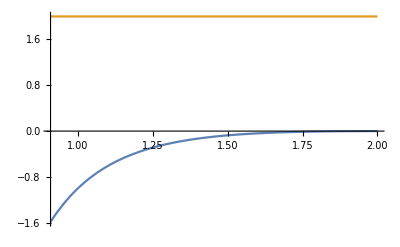

NDSolve::ndsz: At τ == 1.20266, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 1000 steps reached at the point τ == 1.61754.

```mathematica
(*M=10^12*)
(*G=6.67408*10^-11;
ε0=8.85418782×10-12;*)
ε=2;
rs= 1;
l=2*rs;
t1= 2.202660117932665;
r0=2*rs;

RNt1=3;
RNwt0=1.617536122715899;
rq=0.95*rs/2;
RNrp=((rs/2)+Sqrt[(rs/2)^2-rq^2]);
RNrn=((rs/2)-Sqrt[(rs/2)^2-rq^2]);



Plot[{l^2/(rr)^2-rs/(rr)-(rs*l^2)/(rr)^3,ε},{rr,rs/1.1,r0},PlotRange->All]

transform=CoordinateTransformData["Polar"->"Cartesian","Mapping"];

s=First@NDSolve[{D[r[τ],τ]==-Sqrt[ε-(1-(rs/r[τ]))(1+l^2/r[τ]^2)],r[0]==r0},r,{τ,0,t1},MaxSteps->1000];
ϕ[τ_]:=NIntegrate[l/(r[t]/.s)^2,{t,0,τ}];

plot=ParametricPlot[transform[Evaluate[{r[τ]/.s,ϕ[τ]}]],{τ,0,t1},PlotStyle->Red];
scr=ParametricPlot[{rs*Cos[τ],rs*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightRed];




RNs=First@NDSolve[{D[r[τ],τ]==-Sqrt[ε-(1-(rs/r[τ])+(rq^2/r[τ]^2))(1+l^2/r[τ]^2)],r[0]==r0},r,{τ,0,RNt1},MaxSteps->1000];
RNws=First@NDSolve[{D[r[τ],τ]==Sqrt[ε-(1-(rs/r[τ])+(rq^2/r[τ]^2))(1+l^2/r[τ]^2)],r[RNwt0]==Re[r[RNwt0]/.RNs]+Re[r[RNwt0]/.RNs]/10000},r,{τ,RNwt0,RNt1},MaxSteps->1000];

RNϕ[τ_]:=NIntegrate[l/(r[t]/.RNs)^2,{t,0,τ}];
RNwϕ[τ_]:=NIntegrate[l/(r[t]/.RNws)^2,{t,0,τ}];

RNplot=ParametricPlot[transform[Evaluate[{r[τ]/.RNs,RNϕ[τ]}]],{τ,0,RNt1},PlotStyle->Blue];
RNwplot=ParametricPlot[transform[Evaluate[{r[τ]/.RNws,RNϕ[RNwt0]+RNwϕ[τ]}]],{τ,RNwt0,RNt1},PlotStyle->Blue];
RNrpPlot=ParametricPlot[{RNrp*Cos[τ],RNrp*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightBlue];
RNrnPlot=ParametricPlot[{RNrn*Cos[τ],RNrn*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightBlue];




fplot=Show[RNplot,RNwplot,RNrpPlot,RNrnPlot,plot,scr,PlotRange->All]

(*Plot[l^2/(r[τ]/.s)^2-rs/(r[τ]/.s)-(rs*l^2)/(r[τ]/.s)^3,{τ,0,t1},PlotRange->All]*)
(*Plot[r[τ]/.s,{τ,0,t1}]
Plot[ϕ[τ],{τ,0,t1}]*)
(*Plot[r[τ]/.qs,{τ,0,t1q}]
Plot[qϕ[τ],{τ,0,t1q}]*)
```

```mathematica
Export["C:\Users\mogzy\OneDrive - Swansea University\Dis\Task 4.2 plots\ε="<>ToString[ε]<>", rs="<>ToString[rs]<>", l="<>ToString[l]<>", r0="<>ToString[r0]<>", rq="<>ToString[rq]<>".png",fplot]
```

C:\Users\mogzy\OneDrive - Swansea University\Dis\Task 4.2 plots\ε=2, rs=1, l=2, r0=2, rq=0.475.png